# Unit Ramp

```mathematica
RampFunction[t_]=t UnitStep[t]
```

t UnitStep[t]

```mathematica
Piecewise[{{t,t>=0}},0]
```

Piecewise[{{t, t≥0}, {0, True}}]

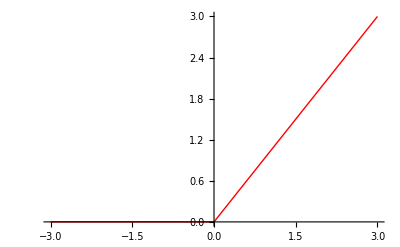

```mathematica
Plot[RampFunction[t],{t,-3,3},PlotStyle->{Red,Thick}]
```

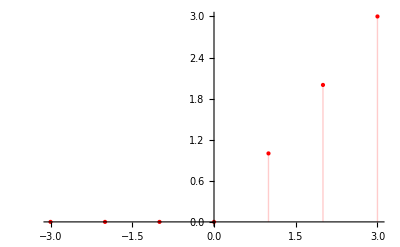

```mathematica
DiscretePlot[RampFunction[n],{n,-3,3,1},PlotMarkers->{"Point",Large},PlotStyle->Red]
```